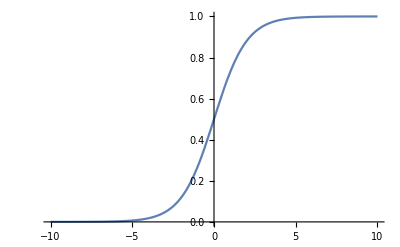

```mathematica
ss0[x_] := 1/(1+Exp[-x]);
Plot[ss0[x],{x,-10,10}]
```

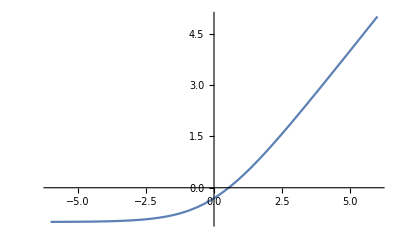

```mathematica
ss0[x_] := Max[{0,x}]
ss0[x_] := Log[1+Exp[x]]
ss0[x_] := x^3
ss0[x_] := 0.05*x  +0.95*Log[1+Exp[x]]
ss0[x_] := Log[1+Exp[x]]-1
Plot[ss0[x],{x,-6,6}]
```

## 3 neuron network

One input neuron + one output neuron;  a single neuron in a single hidden layer.
4 parameters:  w11 from input to hidden, b1 for hidden, w21 from hidden to output, b2 for output

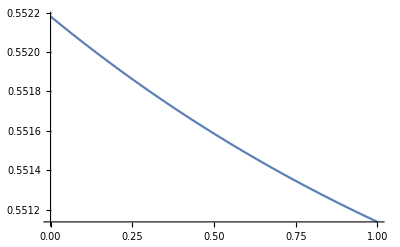

```mathematica
nnfunc3[x_, w11_,w21_,b1_,b2_] :=  ss0[w21*ss0[w11*x+b1] +b2]    (* The effect of the network is this function *)
Plot[nnfunc3[x,0.61,-0.2,3,0.4],{x,0,1}]
```

```mathematica
targetfunc[x_] := x^2;   Plot[targetfunc[x],{x,-1.1,1.1}];  
(* The function we want to use the neural network for *)
xmin = -1;xmax = 1;  xwidth = (xmax-xmin);    (*  Set range of x *)
```

```mathematica
nT=100.0 ; (* Integral discretized into nT intervals; nT+1 test/training values *)
xvec = Table[x,{x,xmin,xmax,xwidth/nT}]     
(* This is either/both the training set or the test set.   *)
LL0[w11_,w21_,b1_,b2_] := (xwidth/nT)*Sum[(nnfunc3[xvec[[ii]],w11,w21,b1,b2]-targetfunc[xvec[[ii]]])^2,{ii,1,Length[xvec]}]
(* The loss function.  This is what we will minimize.  *)
HH[w1_,w2_,b1_,b2_]:=D[LL0[w1,w2,b1,b2],{{w1,w2,b1,b2},2}]   (* Hessian of the loss function *)
```

{-1.,-0.98,-0.96,-0.94,-0.92,-0.9,-0.88,-0.86,-0.84,-0.82,-0.8,-0.78,-0.76,-0.74,-0.72,-0.7,-0.68,-0.66,-0.64,-0.62,-0.6,-0.58,-0.56,-0.54,-0.52,-0.5,-0.48,-0.46,-0.44,-0.42,-0.4,-0.38,-0.36,-0.34,-0.32,-0.3,-0.28,-0.26,-0.24,-0.22,-0.2,-0.18,-0.16,-0.14,-0.12,-0.1,-0.08,-0.06,-0.04,-0.02,0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.}

```mathematica
(*  Minimization attempts *)
sol0 = FindMinimum[LL0[w11, w21,b1,b2], {{w11,10.1}, {w21,-1.9},{b1,-0.6},{b2,-0.01}}, MaxIterations->10000, Method->"ConjugateGradient"]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.119308,{w11→10.4274,w21→-3.95433,b1→8.58521,b2→2.88911}}

```mathematica
LL0[w11,w21,b1,b2] /. sol0[[2]]
Eigenvalues[HH[w11,w21,b1,b2] /. sol0[[2]]]
```

0.119308

{0.287559,0.0247025,0.000377418,0.0000515044}

```mathematica
LL0[-10.43, 3.954, -8.585, +10.065]
```

1.06656

```mathematica
Plot[{nnfunc3[x,-10.43, 3.954, -8.585, +10.065] , targetfunc[x]},{x,xmin-0.1*xwidth,xmax+0.1*xwidth}];
```

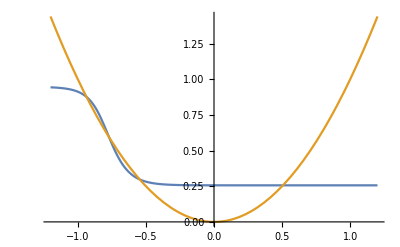

```mathematica
Plot[{(nnfunc3[x,w11,w21,b1,b2] /. sol0[[2]]), targetfunc[x]},{x,xmin-0.1*xwidth,xmax+0.1*xwidth}]
```

```mathematica
l01 = Table[{x, (nnfunc3[x,w11,w21,b1,b2] /. sol0[[2]]), targetfunc[x]}, {x,xmin,xmax, xwidth/(2.0*nT)}];
Export["tttest.dat",l01];
strm=OpenAppend["tttest.dat"];WriteString[strm,"\n"];Close[strm]
```

tttest.dat

```mathematica
sol0 = FindMinimum[LL0[w11, w21,b1,b2], {{w11,75}, {w21,3.96},{b1,-60},{b2,-1}}, MaxIterations->1000]
```

{0.119308,{w11→10.4274,w21→3.95432,b1→-8.58523,b2→-1.06522}}

```mathematica
sol0 = FindMinimum[LL0[w11, w21,b1,b2], {{w11,RandomReal[{-10,20}]}, {w21,RandomReal[{200,-100}]},{b1,RandomReal[{-32,32}]},{b2,RandomReal[{-20,20}]}}, MaxIterations->1000]
```

{0.420267,{w11→-2.88776,w21→-38.644,b1→30.5068,b2→11.3132}}

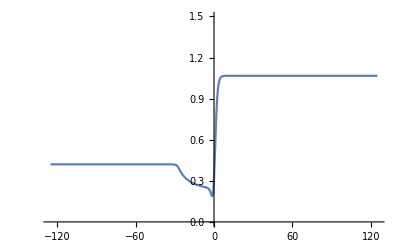

```mathematica
Plot[LL0[ +10.43, 30.954, -8.585, b2], {b2,-125,125}, PlotRange->{0,1.5}]
```

```mathematica
l01 = Table[{vv, LL0[ vv, 3.954,  -8.585,10]}, {vv,-80,80,0.2}];
Export["tttest.dat",l01];
strm=OpenAppend["tttest.dat"];WriteString[strm,"\n"];Close[strm]
```

tttest.dat

```mathematica
Plot[LL0[0.14446, w21,11.69, -316], {w21,20,28}]
```

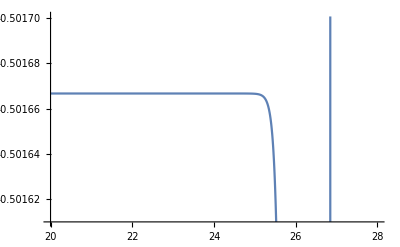

DensityPlot::cfun: Value of option ColorFunction -> Blue is not a valid color function, or a gradient ColorData entity.

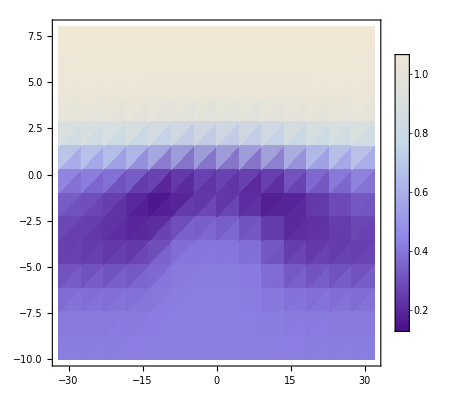

```mathematica
dplt1 = DensityPlot[LL0[w11, 3.954,-8.585,b2], {w11,-32,32},{b2,-10,8}, ColorFunction->"Blue",PlotLegends->Automatic]
```

```mathematica
Export["testplot.pdf",dplt1]
```

testplot.pdf

```mathematica
plt3d =Plot3D[LL0[-10.43, 3.954,Subscript[b, 1], Subscript[b, 2]], {Subscript[b, 1],-132,222},{Subscript[b, 2],-25,22},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Export["testplot.pdf",plt3d]
```

testplot.pdf

## Linear 4-neuron network

One input neuron + one output neuron;  two hidden layers, a single neuron in a single hidden layer.
6 parameters:  w1 from input to 1st hidden, b1 for 1st hidden, w2 from 1st hidden to 2nd hidden, b2 for 2nd hidden, w3 for 2nd hidden to output, b3 for output

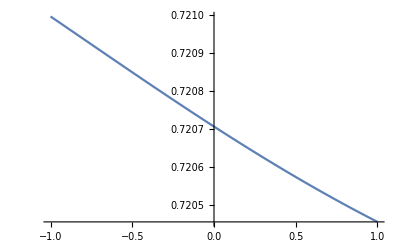

```mathematica
nnfunc4l[x_, w1_,w2_,w3_,b1_,b2_,b3_] :=  ss0[w3*ss0[w2*ss0[w1*x+b1] +b2]+b3]    (* The effect of the network is this function *)
Plot[nnfunc4l[x,0.61,-0.2,3,0.4, -4,0.9],{x,-1,1}]
```

```mathematica
targetfunc[x_] := x^2;   Plot[targetfunc[x],{x,-1.1,1.1}];  
(* The function we want to use the neural network for [target of the regression] *)
xmin = -1;xmax = 1;  xwidth = (xmax-xmin);    (*  Set range of x *)
```

```mathematica
nT=100.0 ; (* Integral discretized into nT intervals; nT+1 test/training values *)
xvec = Table[x,{x,xmin,xmax,xwidth/nT}]     
(* This is either/both the training set or the test set.   *)
LL04l[w1_,w2_,w3_,b1_,b2_,b3_] := (xwidth/nT)*Sum[(nnfunc4l[xvec[[ii]],w1,w2,w3,b1,b2,b3]-targetfunc[xvec[[ii]]])^2,{ii,1,Length[xvec]}]
(* The loss function.  This is what we will minimize.  *)
HH[w1_,w2_,w3_,b1_,b2_,b3_]:=D[LL04l[w1,w2,w3,b1,b2,b3],{{w1,w2,w3,b1,b2,b3},2}]   (* Hessian of the loss function *)
```

{-1.,-0.98,-0.96,-0.94,-0.92,-0.9,-0.88,-0.86,-0.84,-0.82,-0.8,-0.78,-0.76,-0.74,-0.72,-0.7,-0.68,-0.66,-0.64,-0.62,-0.6,-0.58,-0.56,-0.54,-0.52,-0.5,-0.48,-0.46,-0.44,-0.42,-0.4,-0.38,-0.36,-0.34,-0.32,-0.3,-0.28,-0.26,-0.24,-0.22,-0.2,-0.18,-0.16,-0.14,-0.12,-0.1,-0.08,-0.06,-0.04,-0.02,0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.}

```mathematica
(*  Minimization attempts *)
sol4l = FindMinimum[LL04l[w1, w2,w3,b1,b2,b3], {{w1,-10.1}, {w2,-0.429},{w3,3.91},{b1,-8.6},{b2,-8.8},{b3,-1.01}}, MaxIterations->10000, Method->"ConjugateGradient"]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

{0.118712,{w1→-3.54269,w2→89.6749,w3→80.5185,b1→1.23224,b2→-91.9846,b3→-1.06858}}

```mathematica
LL04l[w1,w2,w3,b1,b2,b3] /. sol4l[[2]]
Eigenvalues[HH[w1,w2,w3,b1,b2,b3] /. sol4l[[2]]]
```

0.119309

{147161.,706.525,0.110634,0.000329751,-1.32642×10^-9,8.0864×10^-12}

```mathematica
Eigensystem[HH[w1,w2,w3,b1,b2,b3] /. sol4l[[2]]]
```

{{0.436646,0.105438,0.00853311,0.000127039,3.21341×10^-9,2.0524×10^-9},{{-0.457002,0.391562,0.00507118,0.583409,0.398196,0.372661},{0.180268,-0.197692,-0.00256695,-0.180717,-0.199712,0.925133},{0.0757939,0.516643,0.00681525,-0.680782,0.508505,0.0724397},{-0.867701,-0.201097,-0.00362554,-0.404268,-0.207855,0.00225376},{0.000900936,0.0169205,-0.999851,0.000375728,-0.00342216,5.74295×10^-7},{0.00129534,0.707072,0.0143899,0.00884044,-0.706939,-5.86835×10^-7}}}

```mathematica
LL04l[23,0.1,-10.43, 3.954, -8.585, +10.065]
```

1.06655

```mathematica
Plot[{nnfunc4l[x,-10.43, 3.954, -8.585, -0.1,2,+10.065] , targetfunc[x]},{x,xmin-0.1*xwidth,xmax+0.1*xwidth}];
```

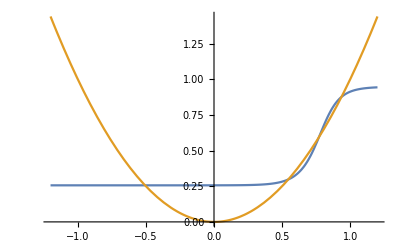

```mathematica
Plot[{(nnfunc4l[x,w1,w2,w3,b1,b2,b3] /. sol4l[[2]]), targetfunc[x]},{x,xmin-0.1*xwidth,xmax+0.1*xwidth}]
```

```mathematica
l01 = Table[{x, (nnfunc3[x,w11,w21,b1,b2] /. sol4l[[2]]), targetfunc[x]}, {x,xmin,xmax, xwidth/(2.0*nT)}];
Export["tttest.dat",l01];
strm=OpenAppend["tttest.dat"];WriteString[strm,"\n"];Close[strm]
```

tttest.dat

```mathematica
(* Another minimization attempt; let computer choose initial values  *)sol4l = FindMinimum[LL04l[w1, w2,w3,b1,b2,b3], {{w1,RandomReal[{-100,200}]}, {w2,RandomReal[{200,-100}]}, {w3,RandomReal[{200,-100}]},{b1,RandomReal[{-32,32}]},{b2,RandomReal[{-32,32}]},{b3,RandomReal[{-20,20}]}}, MaxIterations->1000]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.420267,{w1→83.6881,w2→-11.8591,w3→-68.0229,b1→-3.4584,b2→21.0706,b3→0.138297}}

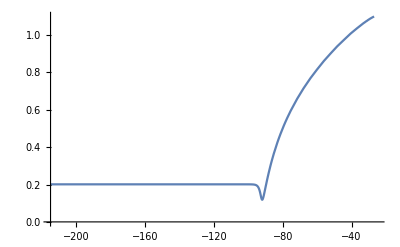

```mathematica
Plot[(LL04l[w1,w2,w3,b1,vv, b3] /. sol4l[[2]]), {vv,-215,-25}, PlotRange->{0,1.1}]
```

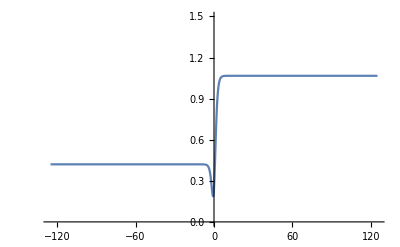

```mathematica
Plot[LL04l[0.1,3.2, +10.43, 30.954, -8.585, b3], {b3,-125,125}, PlotRange->{0,1.5}]
```

```mathematica
l01 = Table[{vv, LL04l[ vv, 3.954,  -8.585,10,4,0.8]}, {vv,-80,80,0.2}];
Export["tttest.dat",l01];
strm=OpenAppend["tttest.dat"];WriteString[strm,"\n"];Close[strm]
```

tttest.dat

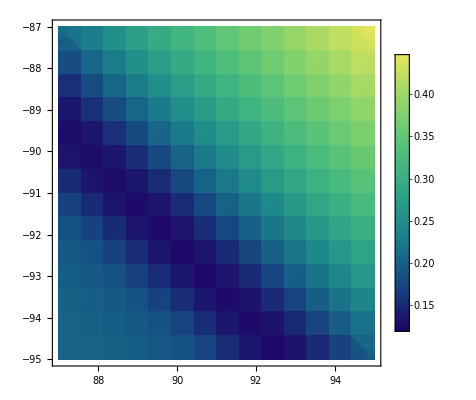

```mathematica
dplt1 = DensityPlot[(LL04l[w1,vvX,w3,b1,vvY, b3] /. sol4l[[2]]), {vvX,87,95},{vvY,-95,-87}, ColorFunction->"BlueGreenYellow",PlotLegends->Automatic]
```

```mathematica
Export["testplot.pdf",dplt1]
```

testplot.pdf

```mathematica
plt3d =Plot3D[(LL04l[w1,vvX,w3,b1,vvY, b3] /. sol4l[[2]]), {vvX,87,95},{vvY,-95,-87},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
plt3d =Plot3D[LL04l[-10.43, 3.954, 4,Subscript[b, 1], Subscript[b, 2], 0.3], {Subscript[b, 1],-132,222},{Subscript[b, 2],-25,22},AxesLabel->Automatic];
```

```mathematica
Export["testplot.pdf",plt3d]
```

testplot.pdf

## Old effort: 4-neuron diamond network (to be revived)

```mathematica
nnfuncT[x_, w11_,w12_, w21_,w22_,b1_,b2_,b3_] :=  ss0[w21*ss0[w11*x+b1] + w22*ss0[w12*x+b2]+b3]
```

```mathematica
nnfuncT[0.2,0.61,2,0.13,0.4, -1, 1.4]
```

0.821663